{{66572.3,3.42265,50.4993,9.8589,2.63294,3.28686×10^6},{60459.1,3.42454,50.6777,4.08899,2.1315,3.29835×10^6},{58196.1,3.43242,50.4766,2.31108,1.85987,3.28688×10^6},{57236.9,3.42287,50.5956,1.24492,1.83727,3.29128×10^6},{56789.7,3.43185,50.547,0.896443,1.78759,3.29195×10^6}}

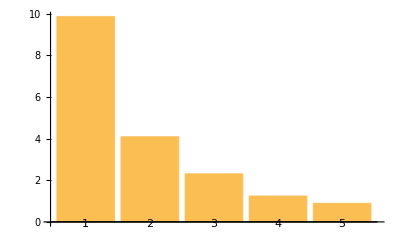

```mathematica
numbersStation=8; (* Кол-во колонок на заправке *)
numbersCashiers = 2; (* Кол-во кассиров на заправке *)
numbersCars=1000; (*Кол-во машин, которые пройдут симуляцию*)
listAllData = {};


activityOnCashbox[]:=Module[{petrol, litters,fuel, products, snack, money, timeOnCashbox, timeOnStation},
petrol = {{"92", 51.16},{"95", 55.62},{"100", 64.06},{"Дт", 51.21}}; (*Виды и цены за литр топлива*)
products = {{"Хот-дог",250},{"Кофе",200},{"Омывайка",500},{"Чипсы",80},{"Лимонад",60},{"Масло",1000},{"Сок",50},{"Бургер",300},{"Мороженое",70},{"Шоколадка",100},{"Орешки",120}};
money=0;
timeOnCashbox = 0; (*Время на кассе*)
litters=RandomInteger[{1, 100}];
fuel=RandomChoice[petrol];
money += litters*fuel[[2]];
timeOnStation = litters;
If[RandomChoice[{"Карта","Наличка"}] == "Карта", timeOnCashbox+= 1, timeOnCashbox += 2];
snack = RandomChoice[{True, False}];
If[snack, For[i = 1, i <= RandomInteger[{1, Length@products}], i++, money+=RandomChoice[products][[2]]; timeOnCashbox+= 1]];
Return[{money, timeOnCashbox, timeOnStation}];
];

gasStationSimulation[numbersStation_,numbersCashiers_,numbersCars_]:=Module[{queueLeft,queueRight,numbersStationUsed,numbersStationFree, queueForCashbox, numbersCashiersUsed, numbersCashiersFree, dataMoney, dataTimeOnCashbox, dataTimeOnStation, dataSupport, dataSupport2, dataTimeQueueOnCashbox,dataTimeQueueOnStation, dataMoneyAll, dataTimeOnCashboxAll, dataTimeOnStationAll, dataTimeQueueOnCashboxAll, dataTimeQueueOnStationAll, dataTimeOnGasStation, counterCar, counterQueue},

(*Переменные*)
queueLeft=0; (*Очередь из машин с правым баком*)
queueRight=0; (*Очередь из манин с левым баком*)
dataMoneyAll = {}; (*Сколько платили все водители за бензин и снеки*)
dataTimeOnCashboxAll = {}; (*Сколько времени все водитель обслуживался на кассе*)
dataTimeOnStationAll = {}; (*Сколько времени все водитель заправлял машину*)
dataTimeQueueOnCashboxAll = {}; (*Сколько времени все водители стояли в очеридна на кассу*)
dataTimeQueueOnStationAll = {};
dataTimeOnGasStation = {};
counterCar = 0;
counterQueue = 0;


(*Симуляция заправки*)
While[counterCar < numbersCars,
(*Переменные*)
dataMoney = {}; (*Сколько платили водители за бензин и снеки*)
dataTimeOnCashbox = {}; (*Сколько времяни водитель обслуживался на кассе*)
dataTimeOnStation = {}; (*Сколько времяни водитель заправлял машину*)
dataTimeQueueOnCashbox = {};
dataTimeQueueOnStation = {};
dataSupport = {}; (*Вспомогательный массив с данными*)
dataSupport2 = {};
result = {};

(*Генерация очереди*)
If[queueLeft + queueRight <  2*numbersStation, 
random = RandomInteger[{2, 10}];
queueLeft+=Round[random/2];
queueRight+=Round[random/2];];

 
numbersStationUsed=0; (*Кол-во занятых колонок*)
numbersStationFree=numbersStation; (*Кол-во свободных колонок*)

numbersCashiersUsed = 0; (*Кол-во занятых кассиров*)
numbersCashiersFree = numbersCashiers; (*Кол-во свободных кассиров*)


If[queueLeft>=numbersStation/2, numbersStationUsed+=numbersStation/2; numbersStationFree-=numbersStation/2;queueLeft-=numbersStation/2,numbersStationUsed+=queueLeft; numbersStationFree-=queueLeft; queueLeft = 0];

If[queueRight>=numbersStation/2, numbersStationUsed+=numbersStation/2; numbersStationFree-=numbersStation/2;queueRight-=numbersStation/2,numbersStationUsed+=queueRight; numbersStationFree-=queueRight; queueRight=0];


counterCar += numbersStationUsed;
queueForCashbox = numbersStationUsed;

(*Симуляция работы кассы*)
While[queueForCashbox != 0,
numbersCashiersUsed = 0;
numbersCashiersFree = numbersCashiers;


If[queueForCashbox >=  numbersCashiers,  numbersCashiersUsed = numbersCashiers; numbersCashiersFree -= numbersCashiers;
queueForCashbox-= numbersCashiers, numbersCashiersUsed = queueForCashbox; numbersCashiersFree -= queueForCashbox; queueForCashbox = 0];


Do[AppendTo[dataSupport, activityOnCashbox[]], {n, numbersCashiersUsed}];];

(*Распределение данных по массивам*)
For[i = 1, i <= Length@dataSupport, i++, AppendTo[dataMoney, dataSupport[[i]][[1]]]; AppendTo[dataTimeOnCashbox, dataSupport[[i]][[2]]]; AppendTo[dataTimeOnStation, dataSupport[[i]][[3]]]];

(*Подсчет времени ожидания водителя в очереди на кассу*)
support=Partition[dataTimeOnCashbox,UpTo[numbersCashiers]];
zero = {};
For[i = 1, i <= Length@support[[1]],i++, AppendTo[zero, 0]];
support = Insert[support, zero, 1];
For[i = 1,  i < Length@support, i++, If[i == 1, AppendTo[dataTimeQueueOnCashbox, support[[i]]], If[i == Length@support-1 ,AppendTo[dataTimeQueueOnCashbox,Take[support[[i]]+dataTimeQueueOnCashbox[[i-1]], Length@support[[i+1]]]], AppendTo[dataTimeQueueOnCashbox,support[[i]]+dataTimeQueueOnCashbox[[i-1]]]]]];

(*Подсчет*)
dataSupport2 = dataTimeOnCashbox+ dataTimeOnStation+Flatten@dataTimeQueueOnCashbox;
dataSupport2 = Sort[dataSupport2];
For[i = 0, i < numbersStationUsed - counterQueue, i++, AppendTo[dataTimeQueueOnStation, 0]];
counterQueue =Min[queueLeft + queueRight, numbersStation];
If[counterCar < numbersCars , For[i = 1, i <= counterQueue, i++, AppendTo[dataTimeQueueOnStation, dataSupport2[[i]]]]];

(*Добавление данных в общие массивы данных*)
AppendTo[dataMoneyAll, dataMoney];
AppendTo[dataTimeOnCashboxAll, dataTimeOnCashbox];
AppendTo[dataTimeOnStationAll, dataTimeOnStation];
AppendTo[dataTimeQueueOnCashboxAll, dataTimeQueueOnCashbox];
AppendTo[dataTimeQueueOnStationAll, dataTimeQueueOnStation ];
];
AppendTo[result, Total[Flatten@dataTimeOnCashboxAll + Flatten@dataTimeOnStationAll + Flatten@dataTimeQueueOnCashboxAll+  Flatten@dataTimeQueueOnStationAll]];
AppendTo[result,N[Total[Flatten@dataTimeOnCashboxAll]/Length@Flatten@dataTimeOnCashboxAll]];
AppendTo[result,N[Total[Flatten@dataTimeOnStationAll]/Length@Flatten@dataTimeOnStationAll]];
AppendTo[result,N[Total[Flatten@dataTimeQueueOnCashboxAll]/Length@Flatten@dataTimeQueueOnCashboxAll]];
AppendTo[result,N[Total[Flatten@dataTimeQueueOnStationAll]/Length@Flatten@dataTimeQueueOnStationAll]];
AppendTo[result,N[Total[Flatten@dataMoneyAll]]];

Return[result]
];

chartLabels={};
Do[ simulator = {}; (*numbersStation=2*n*)numbersCashiers = n;
AppendTo[chartLabels,numbersCashiers];
Do[AppendTo[simulator, gasStationSimulation[numbersStation,numbersCashiers,numbersCars]], {n, 100}];
AppendTo[listAllData,N[Total[simulator]/Length@simulator]], {n, 5}];
listAllData

AllValue={};
For[i=1,i<=Length@listAllData,i++,AppendTo[AllValue,listAllData[[i]][[4]]]]
BarChart[AllValue,ChartLabels->{chartLabels}]
```